# Лабораторная работа 7

Вариант 10

```mathematica
n=100;
l=1;
tmax=1;
smax=100;
h=N[l/n];
τ=N[tmax/smax];
"уравнение субдиффузии";
eqn[s_,β_]:=Table[1/τ^β ∑_(j=0)^s ((-1)^j Gamma[β+1])/(Gamma[j+1] Gamma[β-j+1]) (y[i,s-j]-y[i,0])-1/h^2 (y[i+1,s]-2 y[i,s]+y[i-1,s])==0,{i,1,n-1}]
Y[s_]:=Table[y[i,s],{i,1,n-1}];
```

```mathematica
"РАЗНЫЕ моменты времени";
```

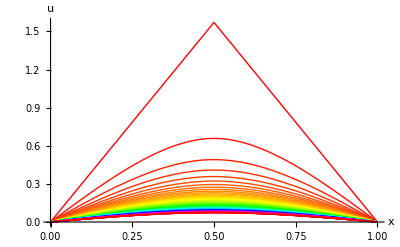

```mathematica
Clear[y];
β=0.5;
u0[x_]=N[ArcSin[Sin[π x]]];

Do[y[i,0]=u0[h i],{i,1,n-1}];
Do[y[0,s]=0;y[n,s]=0,{s,0,smax}]

Clear[s]
For[s=0,s<smax,s++,{B,A}=CoefficientArrays[eqn[s+1,β],Y[s+1]];
yy=LinearSolve[A,-B];
Do[y[i,s+1]=yy[[i]],{i,1,n-1}]];
Show[Table[ListPlot[Table[{i*h,y[i,s]},{i,0,n}],Joined->True,PlotStyle->Hue[s/smax]],{s,0,smax}],AxesLabel->{"x","u"}]
```

```mathematica
"РАЗНЫЕ β в одной точке";
```

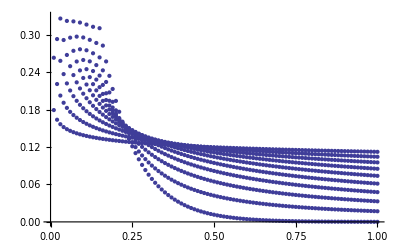

```mathematica
xi={};
u0[x_]=N[ArcSin[Sin[π x]]];
Do[
Clear[y];
β=k/10;
Do[y[i,0]=u0[h i],{i,1,n-1}];
Do[y[0,s]=0;y[n,s]=0,{s,0,smax}];
Clear[s];
Do[{B,A}=CoefficientArrays[eqn[s+1,β],Y[s+1]];
yy=LinearSolve[A,-B];
Do[y[i,s+1]=yy[[i]],{i,1,n-1}],{s,0,smax}];
Do[xi=Append[xi,{s τ,y[IntegerPart[n/2],s]}],{s,0,smax}],{k,1,10}];

ListPlot[xi]
```

```mathematica
"супердиффузия"
```

```mathematica
n=100;
l=1;
tmax=1;
smax=100;
h=N[l/n];
τ=N[tmax/smax];
eqn2[s_,α_]:= Table[1/τ (y2[i,s]-y2[i,s-1])-1/h^α ∑_(j=0)^(i+1) ((-1)^j Gamma[α+1])/(Gamma[j+1] Gamma[α-j+1]) y2[i-j+1,s]==0,{i,1,n-1}]
Y2[s_]:=Table[y2[i,s],{i,1,n-1}]
```

```mathematica
"РАЗНЫЕ моменты времени";
```

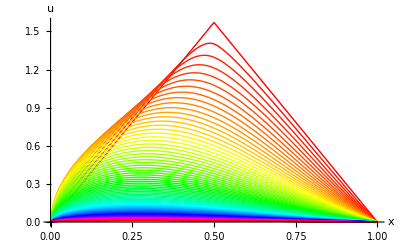

```mathematica
Clear[y2];
α=1.5;
Do[y2[i,0]=u0[h i],{i,1,n-1}];
Do[y2[0,s]=0;y2[n,s]=0,{s,0,smax}]
Clear[s]
Do[
{B,A}=CoefficientArrays[eqn2[s+1,α],Y2[s+1]];
yy2=LinearSolve[A,-B];
Do[y2[i,s+1]=yy2[[i]],{i,1,n-1}],{s,0,smax}];
Show[Table[ListPlot[Table[{i h,y2[i,s]},{i,0,n}],Joined->True,PlotStyle->Hue[s/smax]],{s,0,smax}],PlotRange-> All,AxesLabel->{"x","u"}]
```

```mathematica
"РАЗНЫЕ α в одной точке";
```

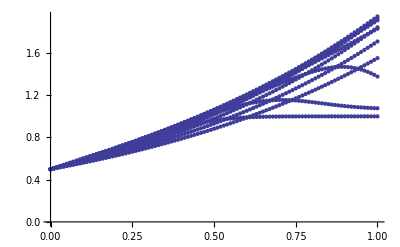

```mathematica
xi2={};
u02[x_]=x;
Do[
Clear[y2];
α=k/10;
Do[y2[i,0]=u02[h i],{i,1,n-1}];
Do[y2[0,s]=0;y2[n,s]=1,{s,0,smax}]
Clear[s]
Do[
{B,A}=CoefficientArrays[eqn2[s+1,α],Y2[s+1]];
yy2=LinearSolve[A,-B];
Do[y2[i,s+1]=yy2[[i]],{i,1,n-1}],{s,0,smax}];
Do[xi2=Append[xi2,{s τ,y2[IntegerPart[n/2],s]}],{s,0,smax}],{k,1,10}]
ListPlot[xi2]
```